```mathematica
b= 20; d=2; rat=0.25; C1=(2/(√2-rat)) (π rat)/(4 b) ; k1=(2/(√2-rat)) (1/b - (π rat)/(4 b));
a[s_] := C1+k1 s
```

```mathematica
sm[sn_]:=(C1+sn)/(1-k1)
```

```mathematica
a[0]
NSolve[(k1 (1-k1)^n)/(1-(1-k1)^(n+1))==C1,n]
```

0.0168654

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{n→22.5677}}

```mathematica
NSolve[(c k1 (1-c k1)^23)/(1-(1-c k1)^(23+1))==C1,c,Reals, WorkingPrecision->MachinePrecision]
```

{{c→0.96529}}

```mathematica
{{c->1.047871872080895},{c->26.20376881596635}}1.047871872080895
```

```mathematica
(* Determines trapezoid vertical notch spacing. *)
(c k1 (1-c k1)^29)/(1-(1-c k1)^(29+1))/.{c->1.00032143170888}
```

```mathematica
N[%] 0.9652896745422104
```

{{c→0.96529}}

```mathematica
0.01686542290824456 + 0.9652896745422104
```

0.982155

```mathematica
0.9821550974504549
```

```mathematica
(2/(√2-rat))
```

1.7179

```mathematica
N[sm[%]]
```

0.989718

```mathematica
a[1]
k1
```

0.113983

2.08331

```mathematica
%+(%+1)
```

16383

```mathematica
2001 (((12 13)/2) 25+5)
```

3911955

```mathematica
27 20
```

540

```mathematica
20 28 4+20 60
```

3440

```mathematica
20 28 12
```

6720

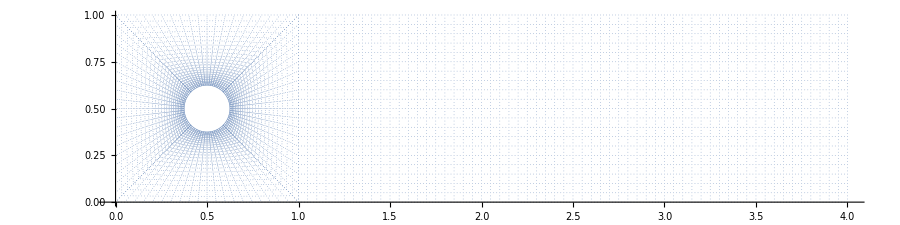

```mathematica
northPos = Import["/home/marko/Dokumenti/MathImports/FluidDynamics/northBlock.dat"];
southPos = Import["/home/marko/Dokumenti/MathImports/FluidDynamics/southBlock.dat"];
westPos = Import["/home/marko/Dokumenti/MathImports/FluidDynamics/westBlock.dat"];
eastPos = Import["/home/marko/Dokumenti/MathImports/FluidDynamics/eastBlock.dat"];
rectPos = Import["/home/marko/Dokumenti/MathImports/FluidDynamics/rectBlock.dat"];
Show[ListPlot[northPos,PlotStyle->AbsolutePointSize[0.02], ImageSize->900,PlotRange->{{-0.01,4.01},{0,1}},AspectRatio->0.25],ListPlot[southPos,PlotStyle->AbsolutePointSize[0.02], ImageSize->400,AspectRatio->0.5],ListPlot[westPos,PlotStyle->AbsolutePointSize[0.02], ImageSize->200,AspectRatio->2],ListPlot[eastPos,PlotStyle->AbsolutePointSize[0.02], ImageSize->200,AspectRatio->2],
ListPlot[rectPos,PlotStyle->AbsolutePointSize[0.02], ImageSize->500,PlotRange->{0,1},AspectRatio->1]]
```

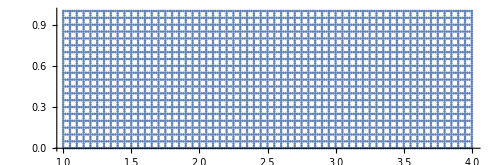

```mathematica
ListPlot[rectPos, ImageSize->500,PlotRange->{0,1},AspectRatio->0.33]
```

```mathematica
lowerLeftX=0.5 (1-√2 0.125) 
lowerLeftY=0.5(1+√2 0.125)
lowerRightX=0.5(1+√2 0.125)
quarterMoonHeight=(1-(√2)/2) 0.125
lowerBoundX[ξ_] := lowerLeftX + (lowerRightX - lowerLeftX) (0.5+Cos[π/4 (3-2 ξ)])/(√2)
lowerBoundY[ξ_] := lowerLeftY + (Sin[π/4 (3-2 ξ)]-1/(√2))/(1-1/(√2)) quarterMoonHeight
```

0.411612

0.588388

0.588388

0.0366117

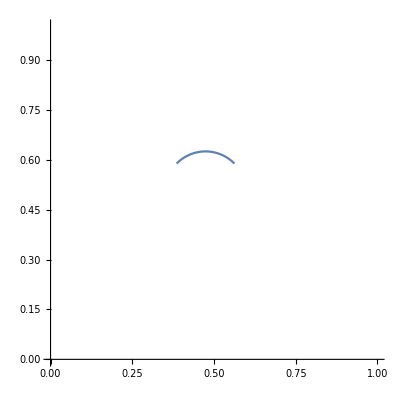

```mathematica
ParametricPlot[{lowerBoundX[ξ], lowerBoundY[ξ]}, {ξ,0,1}, PlotRange->{0,1}]
```

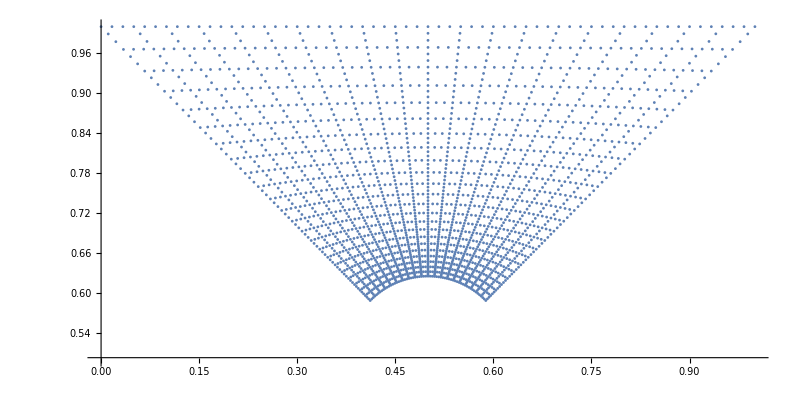

```mathematica
ListPlot[northPos,PlotStyle->AbsolutePointSize[2.0], ImageSize->800,PlotRange->{0.5,1},AspectRatio->0.5]
```